# Trap array algebra

P. Huft

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
(*<<"rbconsts.m"*)
<<"csconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
imag[z_]:=(z-conj[z])/2;
```

## Airy-Gauss beam

```mathematica
A2 = -A0 (a k)/f2(∫_0)^b ⅆρ1 J0[(ρ2 k)/f2 ρ1]J1[(a k)/f1 ρ1]
```

The relation below can be used to evaluate the integral with a power series:

```mathematica
(∫_0)^b dz J0[c z]J1[d z] = (Subscript[Σ, 0]^∞)[(-1)^j/(j!(j+1)!(2j+2))Subscript[F, 1][-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j)]
```

So we have a formula for A2 up to some constant prefactors:

```mathematica
BesselInt[b_,c_,d_,n_]:=Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}];
```

Print out first few terms of I2/I0

```mathematica
(-A0 (a k)/f BesselInt[b,(ρ2 k)/f,(a k)/f,4])^2/A0^2//Expand
```

(a^4 b^4 k^4)/(16 f^4)-(a^6 b^6 k^6)/(128 f^6)+(17 a^8 b^8 k^8)/(36864 f^8)-(5 a^10 b^10 k^10)/(294912 f^10)+(461 a^12 b^12 k^12)/(1061683200 f^12)-(17 a^14 b^14 k^14)/(2123366400 f^14)+(19 a^16 b^16 k^16)/(181193932800 f^16)-(a^18 b^18 k^18)/(1087163596800 f^18)+(a^20 b^20 k^20)/(217432719360000 f^20)-(a^4 b^6 k^6 ρ2^2)/(64 f^6)+(7 a^6 b^8 k^8 ρ2^2)/(3072 f^8)-(11 a^8 b^10 k^10 ρ2^2)/(73728 f^10)+(209 a^10 b^12 k^12 ρ2^2)/(35389440 f^12)-(a^12 b^14 k^14 ρ2^2)/(6553600 f^14)+(179 a^14 b^16 k^16 ρ2^2)/(67947724800 f^16)-(a^16 b^18 k^18 ρ2^2)/(33973862400 f^18)+(a^18 b^20 k^20 ρ2^2)/(5435817984000 f^20)+(5 a^4 b^8 k^8 ρ2^4)/(3072 f^8)-(13 a^6 b^10 k^10 ρ2^4)/(49152 f^10)+(667 a^8 b^12 k^12 ρ2^4)/(35389440 f^12)-(43 a^10 b^14 k^14 ρ2^4)/(56623104 f^14)+(863 a^12 b^16 k^16 ρ2^4)/(45298483200 f^16)-(53 a^14 b^18 k^18 ρ2^4)/(181193932800 f^18)+(13 a^16 b^20 k^20 ρ2^4)/(5435817984000 f^20)-(7 a^4 b^10 k^10 ρ2^6)/(73728 f^10)+(49 a^6 b^12 k^12 ρ2^6)/(2949120 f^12)-(257 a^8 b^14 k^14 ρ2^6)/(212336640 f^14)+(643 a^10 b^16 k^16 ρ2^6)/(13589544960 f^16)-(281 a^12 b^18 k^18 ρ2^6)/(271790899200 f^18)+(31 a^14 b^20 k^20 ρ2^6)/(2717908992000 f^20)+(7 a^4 b^12 k^12 ρ2^8)/(1966080 f^12)-(181 a^6 b^14 k^14 ρ2^8)/(283115520 f^14)+(241 a^8 b^16 k^16 ρ2^8)/(5435817984 f^16)-(329 a^10 b^18 k^18 ρ2^8)/(217432719360 f^18)+(521 a^12 b^20 k^20 ρ2^8)/(21743271936000 f^20)-(13 a^4 b^14 k^14 ρ2^10)/(141557760 f^14)+(7 a^6 b^16 k^16 ρ2^10)/(452984832 f^16)-(17 a^8 b^18 k^18 ρ2^10)/(18119393280 f^18)+(a^10 b^20 k^20 ρ2^10)/(43486543872 f^20)+(11 a^4 b^16 k^16 ρ2^12)/(6794772480 f^16)-(5 a^6 b^18 k^18 ρ2^12)/(21743271936 f^18)+(11 a^8 b^20 k^20 ρ2^12)/(1087163596800 f^20)-(a^4 b^18 k^18 ρ2^14)/(54358179840 f^18)+(a^6 b^20 k^20 ρ2^14)/(543581798400 f^20)+(a^4 b^20 k^20 ρ2^16)/(8697308774400 f^20)

```mathematica
Evaluate[(-A0 (a k)/f BesselInt[b,(ρ2 k)/f,(a k)/f,5])^2/A0^2//Expand]/.b -> f/(a k)BesselJZero[1,1]//N
```

1.9668-(4.1851 ρ2^2)/a^2+(3.67679 ρ2^4)/a^4-(2.53408 ρ2^6)/a^6+(0.978192 ρ2^8)/a^8-(0.0793225 ρ2^10)/a^10+(0.0826177 ρ2^12)/a^12+(0.0572529 ρ2^14)/a^14+(0.034994 ρ2^16)/a^16+(0.00693191 ρ2^18)/a^18+(0.00080106 ρ2^20)/a^20

```mathematica
Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}]/.
```

```mathematica
Sum[1, {i,0,n}]/.n->0
```

1

```mathematica
1.4071425879726265^2
```

1.98005

```mathematica
Clear[a,k,f,b];
(*a = 1*^-4;
k = 2π/(805*^-9);
f=0.1;*)
b =f/(a k)BesselJZero[1,1]//N;
AGterms=(-A0 (a k)/f BesselInt[b,(ρ2 k)/f,(a k)/f,50])^2/A0^2//Expand
```

1.96773-(4.14747 ρ2^2)/a^2+(3.91753 ρ2^4)/a^4-(2.2228 ρ2^6)/a^6+(0.857993 ρ2^8)/a^8-(0.241915 ρ2^10)/a^10+(0.0522214 ρ2^12)/a^12-(0.00892736 ρ2^14)/a^14+(0.00124007 ρ2^16)/a^16-(0.000142836 ρ2^18)/a^18+(0.00001387 ρ2^20)/a^20-(1.15115×10^-6 ρ2^22)/a^22+(8.26142×10^-8 ρ2^24)/a^24-(5.17825×10^-9 ρ2^26)/a^26+(2.85947×10^-10 ρ2^28)/a^28-(1.40173×10^-11 ρ2^30)/a^30+(6.14118×10^-13 ρ2^32)/a^32-(2.41909×10^-14 ρ2^34)/a^34+(8.61403×10^-16 ρ2^36)/a^36-(2.78631×10^-17 ρ2^38)/a^38+(8.22314×10^-19 ρ2^40)/a^40-(2.22321×10^-20 ρ2^42)/a^42+(5.52659×10^-22 ρ2^44)/a^44-(1.26747×10^-23 ρ2^46)/a^46+(2.69018×10^-25 ρ2^48)/a^48-(5.29956×10^-27 ρ2^50)/a^50+(9.71578×10^-29 ρ2^52)/a^52-(1.6618×10^-30 ρ2^54)/a^54+(2.65799×10^-32 ρ2^56)/a^56-(3.98424×10^-34 ρ2^58)/a^58+(5.60842×10^-36 ρ2^60)/a^60-(7.42798×10^-38 ρ2^62)/a^62+(9.27295×10^-40 ρ2^64)/a^64-(1.093×10^-41 ρ2^66)/a^66+(1.21834×10^-43 ρ2^68)/a^68-(1.28626×10^-45 ρ2^70)/a^70+(1.28801×10^-47 ρ2^72)/a^72-(1.22499×10^-49 ρ2^74)/a^74+(1.10798×10^-51 ρ2^76)/a^76-(9.54222×10^-54 ρ2^78)/a^78+(7.83418×10^-56 ρ2^80)/a^80-(6.13833×10^-58 ρ2^82)/a^82+(4.59496×10^-60 ρ2^84)/a^84-(3.2895×10^-62 ρ2^86)/a^86+(2.25433×10^-64 ρ2^88)/a^88-(1.4803×10^-66 ρ2^90)/a^90+(9.32213×10^-69 ρ2^92)/a^92-(5.63487×10^-71 ρ2^94)/a^94+(3.27201×10^-73 ρ2^96)/a^96-(1.82662×10^-75 ρ2^98)/a^98+(9.8111×10^-78 ρ2^100)/a^100-(5.07385×10^-80 ρ2^102)/a^102+(2.52822×10^-82 ρ2^104)/a^104-(1.21463×10^-84 ρ2^106)/a^106+(5.62998×10^-87 ρ2^108)/a^108-(2.51929×10^-89 ρ2^110)/a^110+(1.08899×10^-91 ρ2^112)/a^112-(4.54986×10^-94 ρ2^114)/a^114+(1.83843×10^-96 ρ2^116)/a^116-(7.18806×10^-99 ρ2^118)/a^118+(2.72095×10^-101 ρ2^120)/a^120-(9.97699×10^-104 ρ2^122)/a^122+(3.54538×10^-106 ρ2^124)/a^124-(1.22158×10^-108 ρ2^126)/a^126+(4.08302×10^-111 ρ2^128)/a^128-(1.32445×10^-113 ρ2^130)/a^130+(4.17139×10^-116 ρ2^132)/a^132-(1.27614×10^-118 ρ2^134)/a^134+(3.79379×10^-121 ρ2^136)/a^136-(1.09642×10^-123 ρ2^138)/a^138+(3.08166×10^-126 ρ2^140)/a^140-(8.42668×10^-129 ρ2^142)/a^142+(2.2426×10^-131 ρ2^144)/a^144-(5.8106×10^-134 ρ2^146)/a^146+(1.46625×10^-136 ρ2^148)/a^148-(3.60453×10^-139 ρ2^150)/a^150+(8.6357×10^-142 ρ2^152)/a^152-(2.01721×10^-144 ρ2^154)/a^154+(4.59754×10^-147 ρ2^156)/a^156-(1.0237×10^-149 ρ2^158)/a^158+(2.23179×10^-152 ρ2^160)/a^160-(4.7814×10^-155 ρ2^162)/a^162+(1.01217×10^-157 ρ2^164)/a^164-(2.1326×10^-160 ρ2^166)/a^166+(4.50851×10^-163 ρ2^168)/a^168-(9.62897×10^-166 ρ2^170)/a^170+(2.08355×10^-168 ρ2^172)/a^172-(4.55561×10^-171 ρ2^174)/a^174+(9.98816×10^-174 ρ2^176)/a^176-(2.1734×10^-176 ρ2^178)/a^178+(4.64813×10^-179 ρ2^180)/a^180-(9.63238×10^-182 ρ2^182)/a^182+(2.01789×10^-184 ρ2^184)/a^184-(2.81687×10^-187 ρ2^186)/a^186+(1.78972×10^-189 ρ2^188)/a^188+(8.27474×10^-192 ρ2^190)/a^190+(6.58713×10^-194 ρ2^192)/a^192+(3.0531×10^-196 ρ2^194)/a^194+(1.0207×10^-198 ρ2^196)/a^196+(1.99517×10^-201 ρ2^198)/a^198+(1.79657×10^-204 ρ2^200)/a^200

```mathematica
AGterms = ReplaceAll[AGterms,ρ2->a x]
```

1.96773-4.14747 x^2+3.91753 x^4-2.2228 x^6+0.857993 x^8-0.241915 x^10+0.0522214 x^12-0.00892736 x^14+0.00124007 x^16-0.000142836 x^18+0.00001387 x^20-1.15115×10^-6 x^22+8.26142×10^-8 x^24-5.17825×10^-9 x^26+2.85947×10^-10 x^28-1.40173×10^-11 x^30+6.14118×10^-13 x^32-2.41909×10^-14 x^34+8.61403×10^-16 x^36-2.78631×10^-17 x^38+8.22314×10^-19 x^40-2.22321×10^-20 x^42+5.52659×10^-22 x^44-1.26747×10^-23 x^46+2.69018×10^-25 x^48-5.29956×10^-27 x^50+9.71578×10^-29 x^52-1.6618×10^-30 x^54+2.65799×10^-32 x^56-3.98424×10^-34 x^58+5.60842×10^-36 x^60-7.42798×10^-38 x^62+9.27295×10^-40 x^64-1.093×10^-41 x^66+1.21834×10^-43 x^68-1.28626×10^-45 x^70+1.28801×10^-47 x^72-1.22499×10^-49 x^74+1.10798×10^-51 x^76-9.54222×10^-54 x^78+7.83418×10^-56 x^80-6.13833×10^-58 x^82+4.59496×10^-60 x^84-3.2895×10^-62 x^86+2.25433×10^-64 x^88-1.4803×10^-66 x^90+9.32213×10^-69 x^92-5.63487×10^-71 x^94+3.27201×10^-73 x^96-1.82662×10^-75 x^98+9.8111×10^-78 x^100-5.07385×10^-80 x^102+2.52822×10^-82 x^104-1.21463×10^-84 x^106+5.62998×10^-87 x^108-2.51929×10^-89 x^110+1.08899×10^-91 x^112-4.54986×10^-94 x^114+1.83843×10^-96 x^116-7.18806×10^-99 x^118+2.72095×10^-101 x^120-9.97699×10^-104 x^122+3.54538×10^-106 x^124-1.22158×10^-108 x^126+4.08302×10^-111 x^128-1.32445×10^-113 x^130+4.17139×10^-116 x^132-1.27614×10^-118 x^134+3.79379×10^-121 x^136-1.09642×10^-123 x^138+3.08166×10^-126 x^140-8.42668×10^-129 x^142+2.2426×10^-131 x^144-5.8106×10^-134 x^146+1.46625×10^-136 x^148-3.60453×10^-139 x^150+8.6357×10^-142 x^152-2.01721×10^-144 x^154+4.59754×10^-147 x^156-1.0237×10^-149 x^158+2.23179×10^-152 x^160-4.7814×10^-155 x^162+1.01217×10^-157 x^164-2.1326×10^-160 x^166+4.50851×10^-163 x^168-9.62897×10^-166 x^170+2.08355×10^-168 x^172-4.55561×10^-171 x^174+9.98816×10^-174 x^176-2.1734×10^-176 x^178+4.64813×10^-179 x^180-9.63238×10^-182 x^182+2.01789×10^-184 x^184-2.81687×10^-187 x^186+1.78972×10^-189 x^188+8.27474×10^-192 x^190+6.58713×10^-194 x^192+3.0531×10^-196 x^194+1.0207×10^-198 x^196+1.99517×10^-201 x^198+1.79657×10^-204 x^200

Equate the first few terms of a Gaussian to those of the Airy-Gauss pattern and solve.

```mathematica
nmax = 2;
Series[(AGterms/.x-> 0)Exp[-2 x^2/a^2],{x,0,nmax}]-Series[AGterms,{x,0,nmax}]
```

(4.14747-3.93547/a^2) x^2+O[x]^3

```mathematica
NSolve[(4.1474697060250625-3.935467844463585/a^2) x^2==0,a]
```

{{a→-0.974107},{a→0.974107}}

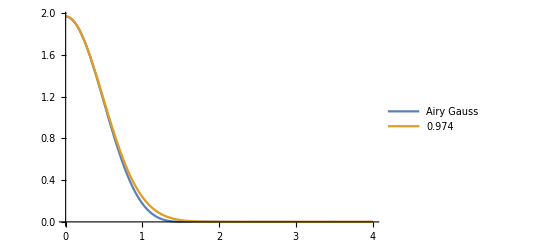

```mathematica
avals = {0.974};
leg = Join[{"Airy Gauss"},avals];
plt=Plot[Evaluate[Join[{AGterms},(AGterms/.x-> 0)Table[Exp[(-2 x^2)/a^2],{a,avals}]]],{x,0,4},PlotLegends->leg]
```

```mathematica
SetDirectory[NotebookDirectory[]];
xpts = Range[0,4,0.01];
data={Table[AGterms,{x,xpts}],xpts};
Export["airygauss.csv",data];
```

## Fourier filtering

Filtering efficiency  of the Fourier aperture or “iris”

```mathematica
Integrate[x BesselJ[0,k x],{x,0,u}]
```

(u BesselJ[1,k u])/k

This is the Airy disk, after setting the circular aperture size and propagation distance (or lens focal length) to 1:

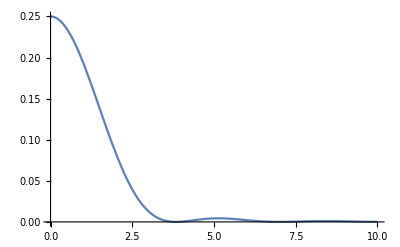

```mathematica
Plot[(BesselJ[1,k ]/k)^2,{k,0.0001,10}]
```

```mathematica
norm = Integrate[k(BesselJ[1,k ]/k)^2,{k,0,∞}]
```

1/2

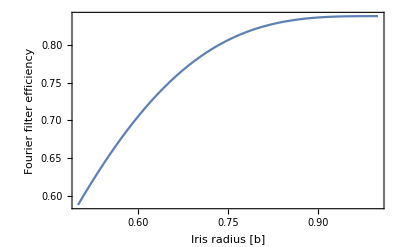

```mathematica
Plot[Integrate[k(BesselJ[1,k ]/k)^2,{k,0,α b}]/norm,{α,0.5,1},Frame->True,Axes->False,FrameLabel->{"Iris radius [b]","Fourier filter efficiency"}]
```

```mathematica
Integrate[k(BesselJ[1,k ]/k)^2,{k,0,α b}]/norm/.α->0.72
```

0.79276

```mathematica
α=1-BesselJ[0,BesselJZero[1,1]];
(-1-√(1-(1-α)^2))/α//N
```

-1.36538

The center of trap intensity (|A_2(0)/A_0|^2) as a function of the background and aperture transmission amplitudes, t_b and t_a (taken to be real), and relative phase between them, ϕ, is given below. This was derived by setting t_a -> t_a e^iϕ in Mark’s derivation.

```mathematica
η=tb^2+2tb(ta Cos[ϕ]-tb)α+(ta^2+tb^2-2ta tb Cos[ϕ])α^2;
NSolve[Evaluate[η/.{tb->1,ϕ->0}]==0,ta]
```

{{ta→0.287119},{ta→0.287119}}

```mathematica
Clear[α]
η=tb^2+2tb(ta Cos[ϕ]-tb)α+(ta^2+tb^2-2ta tb Cos[ϕ])α^2;
NSolve[Evaluate[η/.{tb->1,ϕ->0}]==0,ta]
```

{{ta→(-1.+α)/α},{ta→(-1.+α)/α}}

```mathematica
Collect[η/.tb->1,ta]
```

1-2 α+α^2+ta^2 α^2+ta (2 α Cos[ϕ]-2 α^2 Cos[ϕ])

```mathematica
NSolve[Evaluate[η/.{tb->1}]==0,ta]//TrigToExp//FullSimplify
```

{{ta→(ⅇ^(-ⅈ ϕ) (-1.+1. α))/α},{ta→(ⅇ^(ⅈ ϕ) (-1.+1. α))/α}}

```mathematica
α=1-BesselJ[0,BesselJZero[1,1]];
(ⅇ^(-ⅈ ϕ) (-1.+1. α))/α/.ϕ->0
```

0.287119

```mathematica
α//N
```

1.40276

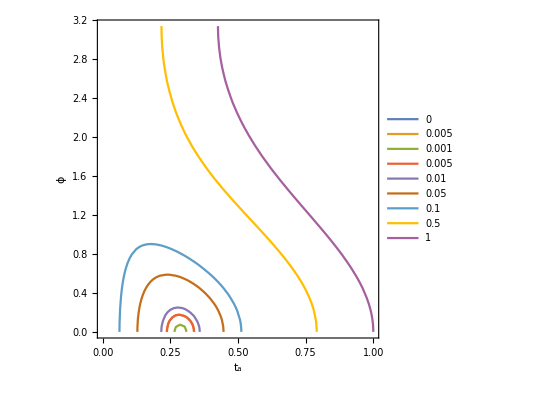

```mathematica
η=1-2 α+α^2+ta^2 α^2+ta (2 α Cos[ϕ]-2 α^2 Cos[ϕ]);
eff={0,0.005,0.001,0.005,.01,0.05,0.1,0.5,1};ContourPlot[Evaluate[Table[η==i,{i,eff}]],{ta,0,1},{ϕ,0,π},FrameLabel->{"t_a","ϕ"},LabelStyle->Directive[Black, Medium],PlotLegends->eff]
```

Repeat this, but find show that the optimal value of ta,phi depend on the choice of iris radius. Go back to where the assumption of b=x1 is made and let that be varied. Think about how to plot this.

## Trap depth

Dark trap:

```mathematica
Tfort = 0.001;
P = 0.150; (*watts*)
λ =8.25*^-7;
d0 = 430*^-6;
datoms  =3*^-6;
M = datoms/d0; (*3 um period at atoms, 430 um at mask*)
ωD2 =(2π c)/λD2;
Δ=c/λD2^2 Abs[λ-λD2]; (*freq detuning from wavelength detuning*)
Ufort = (3π)/2(c^2 ΓD2)/(ωD2^3 Δ)Ifort;
Ifort = kB Tfort((3π)/2(c^2 ΓD2)/(ωD2^3 Δ))^-1;
I0 = M^2 Ifort;
"radius of circular beam on mask, mm"
r = √(P/(π I0));
1000 r
"side of a square beam on mask, mm"
s = √(P/I0);
1000 s
"number of sites along row of a square:"
Floor[s/d0-1]
```

radius of circular beam on mask, mm

3.74756

side of a square beam on mask, mm

6.64238

number of sites along row of a square:

14

Trap depth for a given peak intensity with Gaussian illumination

```mathematica
P = 0.26; (*power before JenOptik objective*)
mThorcam =50/60;(*magnification to the thorcam, from intermediate image*)
mAtoms=(30/200)(22.3/150);(*magnification to the atoms, from intermediate image*)
"Gaussian envelope at atoms, μm"
wTrap = 555.202*^-6/mThorcam*mAtoms;(*width of the Gaussian envelope of the entire array, at the atoms, from Thorcam fit image*)
wTrap*10^6
"Gaussian trap waist at atoms, μm"
w0=87.4047*^-6/mThorcam*mAtoms;(*estimated trap Gaussian waist, from Thorcam fit image*)
w0*10^6
zR = (π w0^2)/λ;
Ifort = (2P)/(π wTrap^2);
Ufort = (3π)/2(c^2 ΓD2)/(ωD2^3 Δ)Ifort;
"Maximum Trap depth, mK"
Ufort/kB/1*^-3
"Radial trap frequency, kHz"
2/(2π w0)√(Ufort/mCs)/1*^3
"Axial trap frequency, kHz"
1/(2π zR)√((2Ufort)/mCs)/1*^3
```

Gaussian envelope at atoms, μm

14.8572

Gaussian trap waist at atoms, μm

2.33895

Maximum Trap depth, mK

6.19383

Radial trap frequency, kHz

84.7154

Axial trap frequency, kHz

6.7256

## Effect of spectral incoherence

```mathematica
ZT = (2 d^2)/λ;
dZT=Δλ D[ZT,λ];
zR = π/λ(a f2/f1)^2;
Solve[dZT/zR==1/2,Δλ]
```

{{Δλ→-(a^2 f2^2 π λ)/(4 d^2 f1^2)}}

## Axial and radial profile of trap

## Expansion in ρ,z, assuming|1-Eg|^2

```mathematica
Clear[w,w0,R,η,λ]
zR = π w0^2/λ;
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
(*Assuming[ρ∈Reals&&λ∈Reals&&w0∈Reals&&z∈Reals&&R∈Reals,(1-Eg)conj[1-Eg]//FullSimplify]*)
```

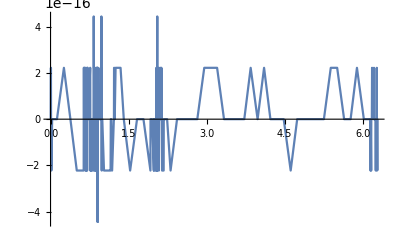

```mathematica
(*check my exact form for the intensity*)
Iexpr  =(1-Eg)conj[1-Eg];
λ = w0=1;
Plot[{Iexpr-(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2])/.ρ->0.001},{z,0,2zR}]
```

```mathematica
Series[(1-Eg)(1-Egc),{z,0,4}]//FullSimplify
```

(-1+ⅇ^(-ρ^2/w0^2))^2+(ⅇ^(-(2 ρ^2)/w0^2) λ^2 (-w0^4+2 w0^2 ρ^2+ⅇ^(ρ^2/w0^2) (2 w0^4-4 w0^2 ρ^2+ρ^4)) z^2)/(π^2 w0^8)+1/(12 π^4 w0^16)ⅇ^(-(2 ρ^2)/w0^2) λ^4 (12 w0^4 (w0^4-4 w0^2 ρ^2+2 ρ^4)-ⅇ^(ρ^2/w0^2) (24 w0^8-96 w0^6 ρ^2+72 w0^4 ρ^4-16 w0^2 ρ^6+ρ^8)) z^4+O[z]^5

```mathematica
%/.ρ->0
```

(λ^2 z^2)/(π^2 w0^4)-(λ^4 z^4)/(π^4 w0^8)+O[z]^5

```mathematica
Series[(1-Eg)(1-Egc),{ρ,0,6}]//FullSimplify
```

(z^2 λ^2)/(π^2 w0^4+z^2 λ^2)-(2 (π^2 w0^2 z^2 λ^2) ρ^2)/((π^2 w0^4+z^2 λ^2)^2)+((π^6 w0^8+3 π^4 w0^4 z^2 λ^2) ρ^4)/((π^2 w0^4+z^2 λ^2)^3)+((-3 π^8 w0^10-6 π^6 w0^6 z^2 λ^2+π^4 w0^2 z^4 λ^4) ρ^6)/(3 (π^2 w0^4+z^2 λ^2)^4)+O[ρ]^7

```mathematica
%/.z-> 0
```

ρ^4/w0^4-ρ^6/w0^6+O[ρ]^7

## Exact profile of Gaussian dark trap

If we assume

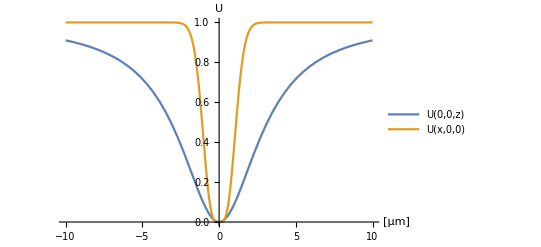

```mathematica
Iexpr  =(1-Eg)conj[1-Eg];
λ =w0=1;
Plot[{(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2])/.{ρ->0.001,z->x},(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2])/.{z->0.001,ρ->x}},{x,-10,10},PlotRange->All,PlotLegends->{"U(0,0,z)","U(x,0,0)"},AxesLabel->{"[μm]","U"}]
```

```mathematica
Plot3D[Iexpr,{ρ,-100,100},{z,-100,100},AxesLabel->{"x","z","U"},PlotRange->All]
```

-Graphics3D-

## Rotated slices

```mathematica
({{ρρ}, {zz}})=({{Cos[x], -Sin[x]}, {Sin[x], Cos[x]}}).({{ρ}, {z}})
```

{{ρ Cos[x]-z Sin[x]},{z Cos[x]+ρ Sin[x]}}

Work in units with zR = w0 = λ=1;

```mathematica
w0=λ=1;
zR = π w0^2/λ;
w=w0(1+(zz/zR)^2)^(1/2);
R=zz(1+zR^2/zz^2);
η=ArcTan[zz/zR];
Idark= 1-2 w0/w Cos[η-π/(R λ)ρρ^2]Exp[-ρρ^2/w^2]+(w0/w)^2 Exp[(-2 ρρ^2)/w^2];
```

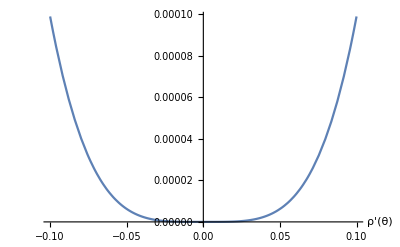
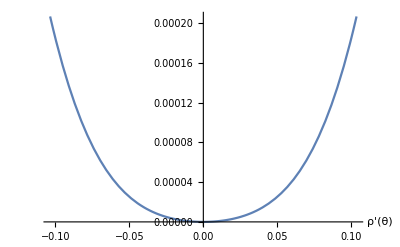
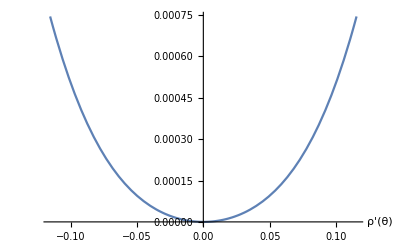
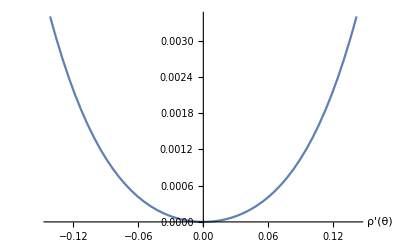

```mathematica
xvals ={0.001,15,30,45};
plts = Table[Plot[Idark/.{ρρ->ρ (Cos[x/180 π]+Tan[x/180 π]Sin[x/180 π]),zz->-ρ Tan[x/180 π]},{ρ,-0.1w0 (Cos[x/180 π]+Tan[x/180 π]Sin[x/180 π]),0.1w0 (Cos[x/180 π]+Tan[x/180 π]Sin[x/180 π])},PlotLegends->StringForm["θ=``",x],AxesLabel->{"ρ'(θ)"}],{x,xvals}]
```

```mathematica
Plot3D[Idark/.{ρρ->ρ,zz->z},{ρ,-2w0,2 w0},{z,-2zR,2zR},AxesLabel->{"x","z","U"},PlotRange->All,LabelStyle->Directive[Bold, Medium]]
```

-Graphics3D-

```mathematica
x=45;(*rotate by 45 degrees*)
Plot3D[Idark/.{ρρ->(ρ +z Sin[x/180 π])/Cos[x/180 π],zz->(z -ρ Sin[x/180 π])/Cos[x/180 π]},{ρ,-10,10},{z,-10,10},AxesLabel->{"x","z","U"},PlotRange->All]
```

-Graphics3D-

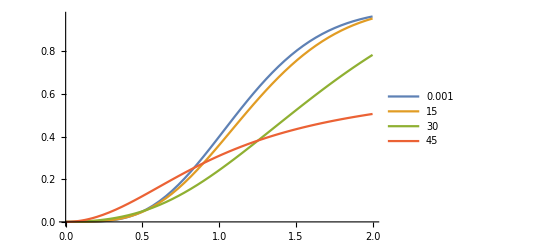

```mathematica
Clear[x];
z = -ρ Tan[x/180 π];
xvals = {0.001,15,30,45};
Plot[Evaluate[Table[Idark/.{ρρ->(ρ + z Sin[x/180 π])/Cos[x/180 π],zz->(z -ρ Sin[x/180 π])/Cos[x/180 π]},{x,xvals}]],{ρ,0,2w0},PlotRange->All,PlotLegends->xvals]
```

```mathematica
Collect[Series[Idark/.{ρρ->(ρ -ρ Tan[θ] Sin[θ])/Cos[θ],zz->(-ρ Tan[θ]-ρ Sin[θ])/Cos[θ]},{ρ,0,4}],ρ]
```

(ρ^2 (Tan[θ]^2+2 Sec[θ] Tan[θ]^2+Sec[θ]^2 Tan[θ]^2))/π^2+1/π^4 ρ^4 (π^4 Sec[θ]^4-2 π^2 Sec[θ]^2 Tan[θ]^2-4 π^2 Sec[θ]^3 Tan[θ]^2-4 π^4 Sec[θ]^3 Tan[θ]^2-2 π^2 Sec[θ]^4 Tan[θ]^2-Tan[θ]^4-4 Sec[θ] Tan[θ]^4+4 π^2 Sec[θ] Tan[θ]^4-6 Sec[θ]^2 Tan[θ]^4+8 π^2 Sec[θ]^2 Tan[θ]^4+6 π^4 Sec[θ]^2 Tan[θ]^4-4 Sec[θ]^3 Tan[θ]^4+4 π^2 Sec[θ]^3 Tan[θ]^4-Sec[θ]^4 Tan[θ]^4-2 π^2 Tan[θ]^6-4 π^2 Sec[θ] Tan[θ]^6-4 π^4 Sec[θ] Tan[θ]^6-2 π^2 Sec[θ]^2 Tan[θ]^6+π^4 Tan[θ]^8)

```mathematica
%/.θ->0
```

ρ^4

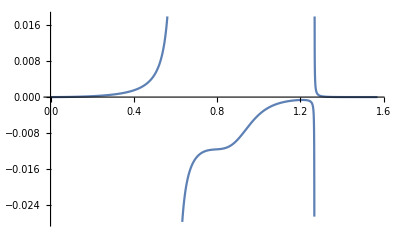

```mathematica
Plot[(Tan[θ]^2+2 Sec[θ] Tan[θ]^2+Sec[θ]^2 Tan[θ]^2)/π^2/(π^4 Sec[θ]^4-2 π^2 Sec[θ]^2 Tan[θ]^2-4 π^2 Sec[θ]^3 Tan[θ]^2-4 π^4 Sec[θ]^3 Tan[θ]^2-2 π^2 Sec[θ]^4 Tan[θ]^2-Tan[θ]^4-4 Sec[θ] Tan[θ]^4+4 π^2 Sec[θ] Tan[θ]^4-6 Sec[θ]^2 Tan[θ]^4+8 π^2 Sec[θ]^2 Tan[θ]^4+6 π^4 Sec[θ]^2 Tan[θ]^4-4 Sec[θ]^3 Tan[θ]^4+4 π^2 Sec[θ]^3 Tan[θ]^4-Sec[θ]^4 Tan[θ]^4-2 π^2 Tan[θ]^6-4 π^2 Sec[θ] Tan[θ]^6-4 π^4 Sec[θ] Tan[θ]^6-2 π^2 Sec[θ]^2 Tan[θ]^6+π^4 Tan[θ]^8),{θ,0,π/2}]
```

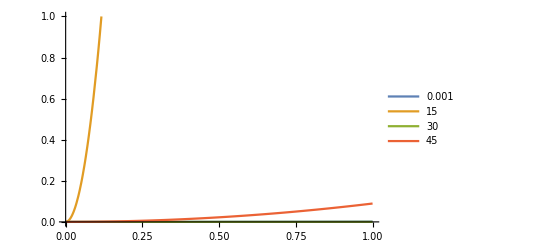

```mathematica
Plot[Evaluate[Table[(ρ^2 (Tan[θ]^2+2 Sec[θ] Tan[θ]^2+Sec[θ]^2 Tan[θ]^2))/π^2,{θ,xvals*180/π}]],{ρ,0,1},PlotLegends->xvals,PlotTheme->"Monochromatic",PlotRange->{0,1}]
```

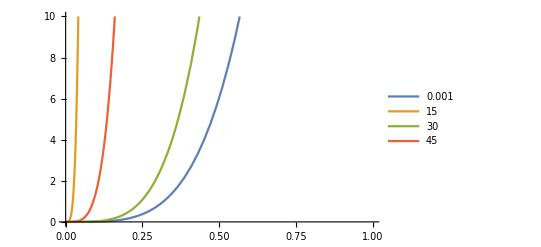

```mathematica
Plot[Evaluate[Table[ρ^4 (π^4 Sec[θ]^4-2 π^2 Sec[θ]^2 Tan[θ]^2-4 π^2 Sec[θ]^3 Tan[θ]^2-4 π^4 Sec[θ]^3 Tan[θ]^2-2 π^2 Sec[θ]^4 Tan[θ]^2-Tan[θ]^4-4 Sec[θ] Tan[θ]^4+4 π^2 Sec[θ] Tan[θ]^4-6 Sec[θ]^2 Tan[θ]^4+8 π^2 Sec[θ]^2 Tan[θ]^4+6 π^4 Sec[θ]^2 Tan[θ]^4-4 Sec[θ]^3 Tan[θ]^4+4 π^2 Sec[θ]^3 Tan[θ]^4-Sec[θ]^4 Tan[θ]^4-2 π^2 Tan[θ]^6-4 π^2 Sec[θ] Tan[θ]^6-4 π^4 Sec[θ] Tan[θ]^6-2 π^2 Sec[θ]^2 Tan[θ]^6+π^4 Tan[θ]^8),{θ,xvals*180/π}]],{ρ,0,1},PlotLegends->xvals,PlotTheme->"Monochromatic",PlotRange->{0,10}]
```

## condition to ensure the trap is harmonic

Taylor expand the integrand for the output field in z, then integrate, keeping b, ta, and phi abstract.

## forces

for simulating dynamics by numerically solving the ODE

```mathematica
Clear[x,zR,w0,λ];
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
```

Bright trap:

```mathematica
fx=D[Eg conj[Eg]/.{ρ-> √(x^2+y^2)},x]
fy=D[Eg conj[Eg]/.{ρ-> √(x^2+y^2)},y]
fz=D[Eg conj[Eg]/.{ρ-> √(x^2+y^2)},z]
```

-(4 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) x)/(w0^2 (1+z^2/zR^2)^2)

-(4 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) y)/(w0^2 (1+z^2/zR^2)^2)

(4 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) (x^2+y^2) z)/(w0^2 (1+z^2/zR^2)^3 zR^2)-(2 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) z)/((1+z^2/zR^2)^2 zR^2)

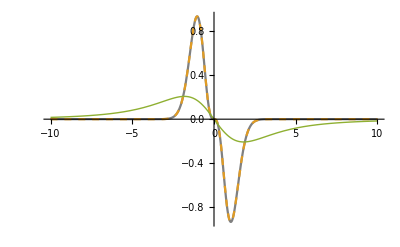

```mathematica
w0=λ=1;
zR = (π w0)/λ;
Plot[{fx/.{x->u,y->0,z->0},fy/.{x->0,y->u,z->0},fz/.{x->0,y->0,z->u}},{u,-10w0,10w0},PlotStyle->{Gray,Dashed,Thick},PlotRange->All]
```

Dark trap, Gaussian approximation. I = |1-Eg|^2, which is given exactly by the expression below.

```mathematica
Clear[zR,λ,w0]
Idark=(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2])
```

1+(ⅇ^(-(2 ρ^2)/(w0^2 (1+z^2/zR^2))))/(1+z^2/zR^2)-(2 ⅇ^(-ρ^2/(w0^2 (1+z^2/zR^2))) Cos[(π ρ^2)/(z (1+zR^2/z^2) λ)-ArcTan[z/zR]])/(√(1+z^2/zR^2))

```mathematica
fx=-D[Idark/.{ρ-> √(x^2+y^2)},x]//FullSimplify
fy=-D[Idark/.{ρ-> √(x^2+y^2)},y]//FullSimplify
fz=-D[Idark/.{ρ-> √(x^2+y^2)},z]//FullSimplify
```

(4 ⅇ^(-(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) x (zR^4-1/λ ⅇ^(((x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) √(1+z^2/zR^2) zR^2 (zR^2 λ Cos[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]]+π w0^2 z Sin[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]])))/(w0^2 (z^2+zR^2)^2)

(4 ⅇ^(-(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) y (zR^4-1/λ ⅇ^(((x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) √(1+z^2/zR^2) zR^2 (zR^2 λ Cos[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]]+π w0^2 z Sin[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]])))/(w0^2 (z^2+zR^2)^2)

(2 ⅇ^(-(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) zR^2 (-2 (x^2+y^2) z zR^2+w0^2 z (z^2+zR^2)+1/λ ⅇ^(((x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) √(1+z^2/zR^2) (-z (-2 (x^2+y^2) zR^2+w0^2 (z^2+zR^2)) λ Cos[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]]+w0^2 (π (x^2+y^2) (z-zR) (z+zR)+zR (z^2+zR^2) λ) Sin[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]])))/(w0^2 (z^2+zR^2)^3)

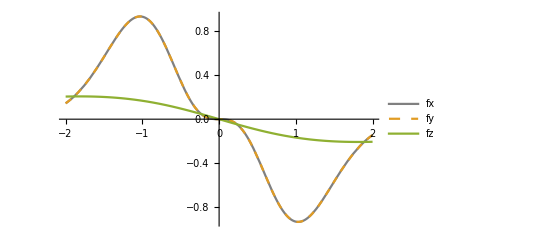

```mathematica
w0=λ=1;
Plot[{fx/.{x->u,y->0,z->0},fy/.{x->0,y->u,z->0},fz/.{x->0,y->0,z->u}},{u,-2w0,2w0},PlotStyle->{Gray,Dashed,Thick},PlotRange->All,PlotLegends->{"fx","fy","fz"}]
```

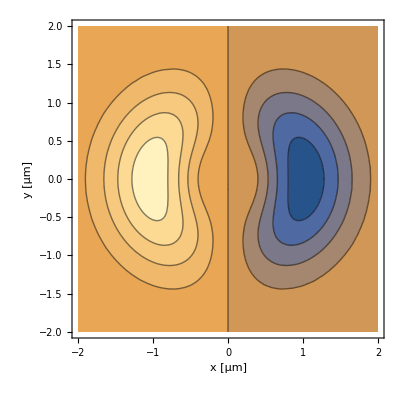
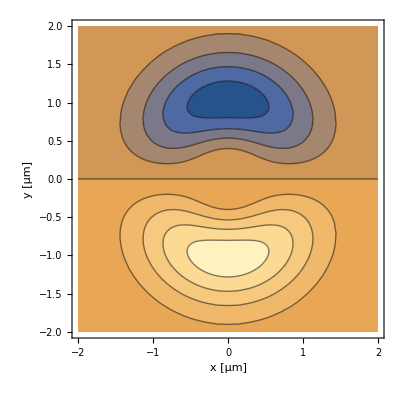
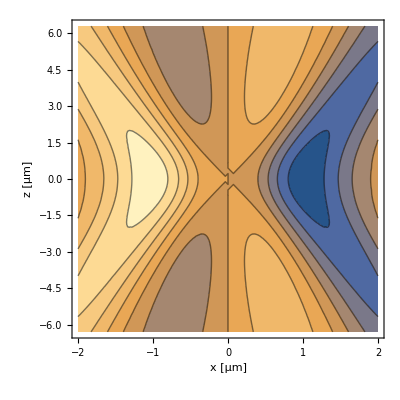
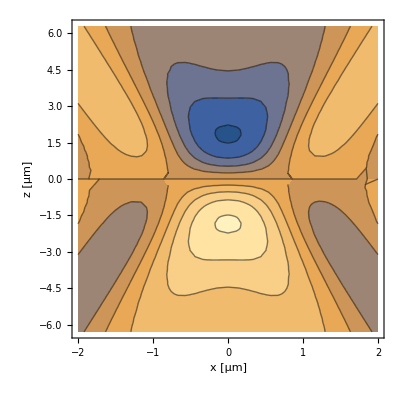
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
w0=λ=1;
GridBox[{{ContourPlot[fx/.z->0,{x,-2w0,2w0},{y,-2w0,2w0},FrameLabel->{"x [μm]","y [μm]"},PlotLegends->"fx"],ContourPlot[fy/.z->0,{x,-2w0,2w0},{y,-2w0,2w0},FrameLabel->{"x [μm]","y [μm]"},PlotLegends->"fy"]},{ContourPlot[fx/.y->0,{x,-2w0,2w0},{z,-2zR,2zR},FrameLabel->{"x [μm]","z [μm]"},PlotLegends->"fx"],ContourPlot[fz/.y->0,{x,-2w0,2w0},{z,-2zR,2zR},FrameLabel->{"x [μm]","z [μm]"},PlotLegends->"fz"]}}]//DisplayForm
```

```mathematica
SetAttributes[withname,HoldFirst];
withname[x_]:={x,SymbolName[Unevaluated@x]};
```

```mathematica
withname[fy]
```

{1/((π^2+z^2)^2)4 ⅇ^(-(2 π^2 (x^2+y^2))/(π^2+z^2)) y (π^4-ⅇ^((π^2 (x^2+y^2))/(π^2+z^2)) π^2 √(1+z^2/π^2) (π^2 Cos[(π (x^2+y^2) z)/(π^2+z^2)-ArcTan[z/π]]+π z Sin[(π (x^2+y^2) z)/(π^2+z^2)-ArcTan[z/π]])),fy}

```mathematica
w0=λ=1;
GridBox[{Table[ContourPlot3D[f[[1]],{x,-2w0,2w0},{y,-2w0,2w0},{z,-2zR,2zR},PlotLegends->f[[2]]],{f,{withname[fx],withname[fy],withname[fz]}}]}]//DisplayForm
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

## confinement and trap frequencies

Gaussian trap

```mathematica
m = mCs;
Clear[w0,T,λ]
λ = .808*^-6;
w0 = 1*^-6;
T = 1.*^-3/ⅇ;

zR = (π w0^2)/λ;
ωx= 2/w0 √((kB T)/m);
ωz=1/zR √((2kB T)/m);
ωz/(2π)
ωx/(2π)
```

8782.2

48289.9

```mathematica
NSolve[{ωx/(2π)==95000,ωz/(2π)==9000},{w0,T}]
```

{{w0→2.46612×10^-6,T→0.00556835}}

```mathematica
Series[1/(1+(z/zR)^2),{z,0,4}]
```

1-z^2/zR^2+z^4/zR^4+O[z]^5

```mathematica
Series[Idark,{z,0,4}]/.ρ->0
```

(λ^2 z^2)/(π^2 w0^4)-(λ^4 z^4)/(π^4 w0^8)+O[z]^5